```mathematica
Mp=250;
L=1;
rp=1;
g=((r^2-rp^2)/L^2);
(*λ=10^-2;*)
```

```mathematica
tor[r_]=SetPrecision[L^2 (-ArcTanh[rp/r]/rp),Mp];
(*∫1/g ⅆr->L^2 (λ^2/(r rp^2)-((rp^2+λ^2) ArcTanh[r/rp])/rp^3)*)
```

```mathematica
D[(-1.`250. ArcTanh[1/r]), r]
```

1./((1-1/r^2) r^2)

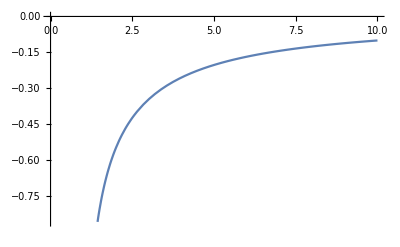

```mathematica
Plot[{tor[r]},{r,rp,10rp},AxesOrigin->{0,0}]
```

```mathematica
exp=Mp-10;
pk=50;
h=1/100;(*grid*)
ts=-2pk;
te=-h;
v0=-pk;
vmax=0;
u0=0;
umax=pk;
k1=(vmax-v0)/h;
k2=(umax-u0)/h;ma=0;
TortStart=v0-umax;
```

```mathematica
ma=0;min=tor[rp+10^-exp];
Do[ts1=10^i;If[-tor[ts1]<h,max=ts1,ma=ma+2],{i,100,2,-1}];
min
ma
(*tor[max];If[tor[max]<te,Print["Aumente os limites de integração, através de vlr"]]*)
```

-276.65678475

2

```mathematica
NRootFinder[Function_,{var_,neg_,pos_},precision_]:=Module[{oldm=neg,n=neg,p=pos,m=(neg+pos)/2,f,g=10^(-precision)},
While[Abs[n-p]>g&&oldm≠m,
oldm=m;
f=Re[Function/.var->m];
If[f>0,p=m,If[f<0,n=m,Break[]]];
m=(n+p)/2;
];
{var->m}
]
```

```mathematica
Timing[tort=Table[SetPrecision[r/. NRootFinder[tor[r]-test,{r,SetPrecision[rp+10^-exp,Mp],SetPrecision[max,Mp]},Mp],Mp],{test,ts,te,h}]; ]
```

Set::wrsym: Symbol tort is Protected.

{122.892,Null}

```mathematica
{236.113489,Null}
```

{236.113,Null}

```mathematica
ListPlot[tort]
```

ListPlot::lpn: tort is not a list of numbers or pairs of numbers.

ListPlot[tort]

```mathematica
ucoord=Table[tor[tort[[i]]],{i,1,Length[tort]}];
ListPlot[ucoord]
```

-Graphics-

```mathematica
Protect[tort];
```